## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalCyclope1D`"
```

```mathematica
methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedNewMethod","ConstrainedCorrelation"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

Get::noopen: Cannot open pyramidalCyclope1DOverConstrained`.

Get::noopen: Cannot open pyramidalCyclope1DConstrainedNewMethod`.

```mathematica
noteBookMode="ConstrainedCorrelation";
```

## Test Points {line1, line2, pyrf12}

```mathematica
dis=1;
```

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1+RandomReal[{-0.05,0.05}],0+RandomReal[{-0.05,0.05}]],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1+RandomReal[{-0.05,0.05}],0+RandomReal[{-0.05,0.05}]],{p,1-dis,30-dis}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,4];
pyrf2=pyrFuncGen[line2,4];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[1,1,1]][x],pyrf12[[1,2,1]][x]},{x,1,30}];
```

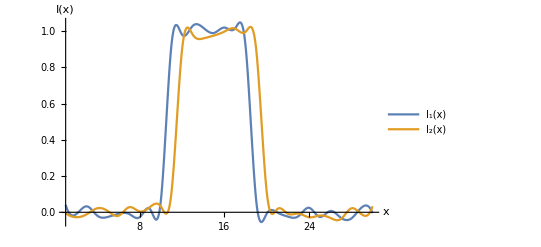

```mathematica
g0=Plot[{pyrf12[[1,1,1]][x],pyrf12[[1,2,1]][x]},{x,1,30},PlotLegends->{Style["I_1(x)",FontSize->fontsize,FontFamily->"Times",Italic],Style["I_2(x)",FontSize->fontsize,FontFamily->"Times",Italic]},AxesLabel->{Style["x",FontSize->fontsize,FontFamily->"Times",Italic],Style["I(x)",FontSize->fontsize,FontFamily->"Times",Italic]}];

convInitial=g0
```

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-initial.pdf"}],convInitial]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\MultipleConvergenceMap1noise-initial.pdf

## Functions

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

```mathematica
(* Creating list of initial Values *)
range={-3,3};
listv0=Select[RandomReal[range,{2500,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
```

## Map Convergence

```mathematica
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && 0<(*Abs[*)Total[x[[1;;2]]](*]*)<dis+1;
```

```mathematica
lvlmin=1;
lvlmax=1;
dis=1;

g0=Grid[Partition[Table[
Labeled[pixelInitialValueGraphics[10,0,0,p,listv0,condition,dis, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),noteBookMode],
Row[{Style["Convergence for p=",FontSize->fontsize,FontFamily->"Times"],Style[p,FontSize->fontsize,FontFamily->"Times",Italic]}]
,Top]
,{p,1,30,5}],3]];
```

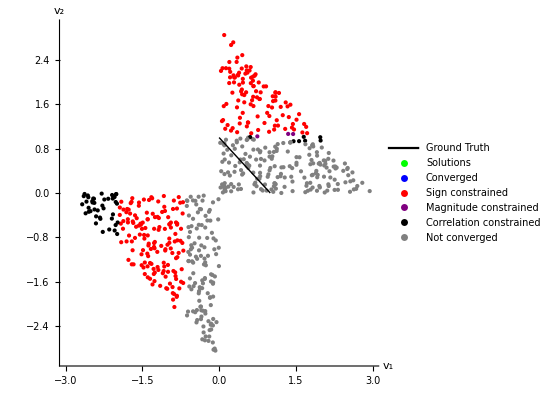
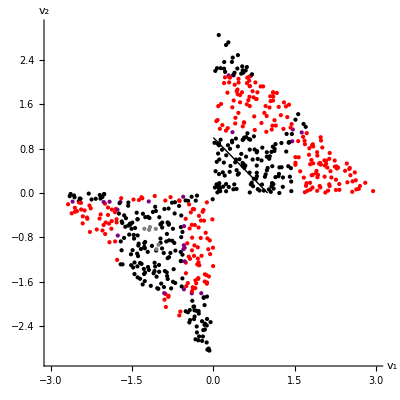
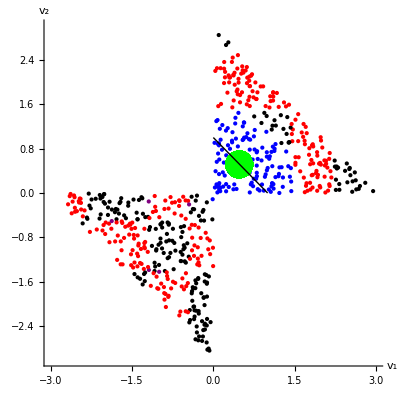
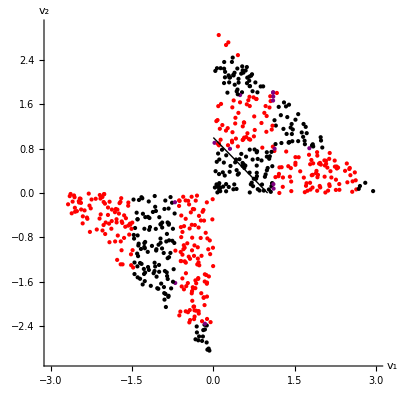
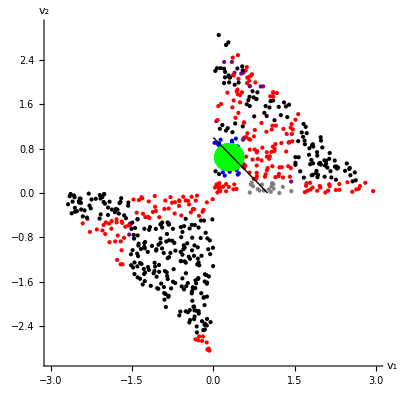
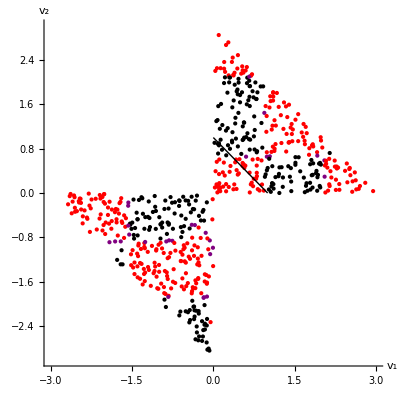
-Graphics-Convergence for p=1 | -Graphics-Convergence for p=6 | -Graphics-Convergence for p=11
-Graphics-Convergence for p=16 | -Graphics-Convergence for p=21 | -Graphics-Convergence for p=26

```mathematica
g0final=Legended[g0,{LineLegend[{Black},{"Ground Truth"}],PointLegend[{Green,Blue,Red,Purple,Black,Gray},{"Solutions","Converged","Sign constrained","Magnitude constrained","Correlation constrained","Not converged"}]}]
```

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];
```

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-map.pdf"}],g0final]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\MultipleConvergenceMap1noise-map.pdf

## Map Convergence

```mathematica
p=11;
```

```mathematica
(* This function is called from pyramidalCyclope1D *)
range={{0.2,0.2}};
g1=Labeled[seeAllLine[0,0,range,condition,Range[p-1,p+1],pyrf12[[lvlmin;;lvlmax]],0.001,noteBookMode],Style[Row[{"[a,b]= [",range[[1,1]],",",range[[1,2]],"]"}],FontSize->fontsize,FontFamily->"Times",Italic],Top];
```

```mathematica
(* This function is called from pyramidalCyclope1D *)
range={{1,1}};
gc=Labeled[seeAllLine[0,0,range,condition,Range[p-1,p+1],pyrf12[[lvlmin;;lvlmax]],0.001,noteBookMode],Style[Row[{"[a,b]= [",range[[1,1]],",",range[[1,2]],"]"}],FontSize->fontsize,FontFamily->"Times",Italic],Top];
```

```mathematica
(* This function is called from pyramidalCyclope1D *)
range={{0.5,2}};

g2=Labeled[seeAllLine[0,0,range,condition,Range[p-1,p+1],pyrf12[[lvlmin;;lvlmax]],0.001,noteBookMode],Style[Row[{"[a,b]= [",range[[1,1]],",",range[[1,2]],"]"}],FontSize->fontsize,FontFamily->"Times",Italic],Top];
```

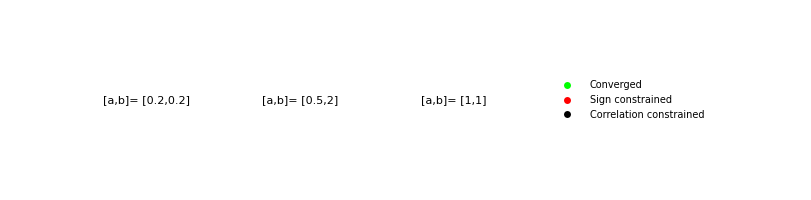
-Graphics-Convergence when v_0∈[a,b] for p= 11

```mathematica
convFinal2=Labeled[Legended[GraphicsRow[{g1,g2,gc},ImageSize->{600,200},Spacings->{-220,-150}],{(*Placed[LineLegend[{LightBlue,LightOrange},{Style["i_a",FontSize->fontsize,FontFamily->"Times",Italic],Style["i_b",FontSize->fontsize,FontFamily->"Times",Italic]}],Below],*)Placed[PointLegend[{Green,Red,Black},{"Converged","Sign constrained","Correlation constrained"}],Right]}],Row[{Style[Row[{"Convergence when "}],FontSize->fontsize,FontFamily->"Times"],Style[Row[{"v_0∈[a,b] "}],FontSize->fontsize,FontFamily->"Times",Italic],Style[Row[{"for "}],FontSize->fontsize,FontFamily->"Times"],Style[Row[{"p= ",p}],FontSize->fontsize,FontFamily->"Times",Italic]}],Top]
```

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-convergence2.pdf"}],convFinal2]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\MultipleConvergenceMap1noise-convergence2.pdf

## Map Convergence

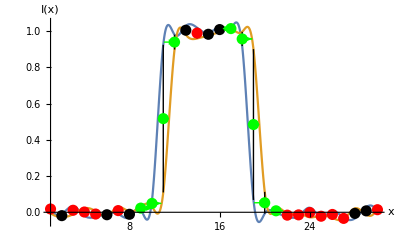
-Graphics-v_0∈[-3,3]

```mathematica
(* This function is called from pyramidalCyclope1D *)
range=listv0;
g11=Labeled[seeAllLine[0,0,range,condition,Range[1,30],pyrf12[[lvlmin;;lvlmax]],0.001,noteBookMode],Style[Row[Style[#, FontSize->25]&/@{"v_0∈[",-3,",",3,"]"}],FontSize->fontsize,FontFamily->"Times",Italic],Top]
```

## Test Points {line1, line2, pyrf12}

```mathematica
dis=1;
```

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1-dis,30-dis}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,4];
pyrf2=pyrFuncGen[line2,4];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[1,1,1]][x],pyrf12[[1,2,1]][x]},{x,1,30}];
```

```mathematica
g0=Plot[{pyrf12[[1,1,1]][x],pyrf12[[1,2,1]][x]},{x,1,30},PlotLegends->{Style["I_1(x)",FontSize->fontsize,FontFamily->"Times",Italic],Style["I_2(x)",FontSize->fontsize,FontFamily->"Times",Italic]},AxesLabel->{Style["x",FontSize->fontsize,FontFamily->"Times",Italic],Style["I(x)",FontSize->fontsize,FontFamily->"Times",Italic]}];

convInitial=g0;
```

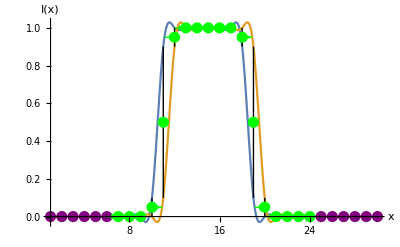
-Graphics-v_0∈[-3,3]

```mathematica
(* This function is called from pyramidalCyclope1D *)
range=listv0;
g1=Labeled[seeAllLine[0,0,range,condition,Range[1,30],pyrf12[[lvlmin;;lvlmax]],0.001,noteBookMode],Style[Row[Style[#, FontSize->25]&/@{"v_0∈[",-3,",",3,"]"}],FontSize->fontsize,FontFamily->"Times",Italic],Top]
```

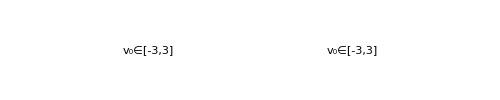

```mathematica
g0final=Legended[GraphicsRow[{g11,g1},ImageSize->{500,100},Spacings->{-300,-200}],Placed[PointLegend[{Green,Red,Purple,Black},Style[#, FontSize->25]&/@{"Converged","Sign constrained","Magnitude constrained","Correlation constrained"}],Right]]
```

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-all.pdf"}],g0final,ImageSize->1000]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\MultipleConvergenceMap1noise-all.pdf